```mathematica
MoreInGraph2[g_]:=IntegerPart[ N[Total[Map[#^5&,N[Eigenvalues[AdjacencyMatrix[g]]]]]]/5!]
```

```mathematica
MoreInGraph3[g_]:=Round[Map[#^3&,N[Eigenvalues[AdjacencyMatrix[g]],200]]//Total]/6
```

```mathematica
samples=Select[Gather[Map[Graph[DeleteDuplicates[Sort/@#]]&,gr],ChromaticPolynomial[#1,x]==ChromaticPolynomial[#2,x]&],Length[#]≠1&];
```

```mathematica
samples//Length
```

1080

```mathematica
AdjacencyMatrix[samples[[1,1]]]
```

SparseArray[<14>, {8, 8}]

```mathematica
Tr[AdjacencyMatrix[samples[[2,1]]]]
```

0

```mathematica
SquaresInGraph[g_]:=Round[ N[Total[Map[#^4&,N[Eigenvalues[AdjacencyMatrix[g]]]]]]/4!]
```

```mathematica
Mean[Map[Table[Round[ N[Total[Map[#^k&,N[Eigenvalues[AdjacencyMatrix[#]]]]]]/k!],{k,{2,3}}]&,s]]
```

{8,1}

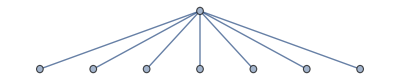
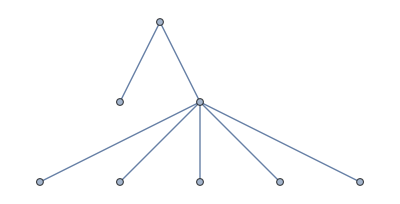
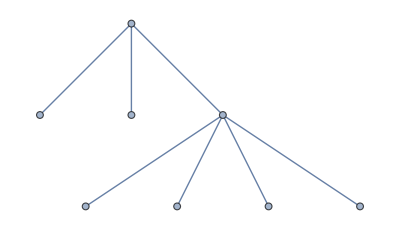
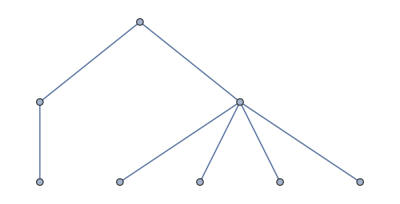
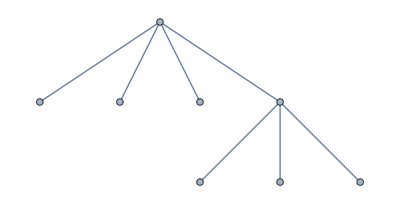
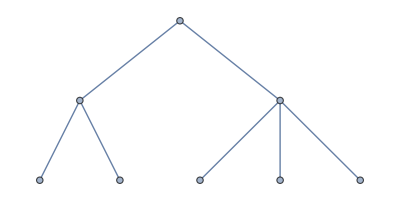
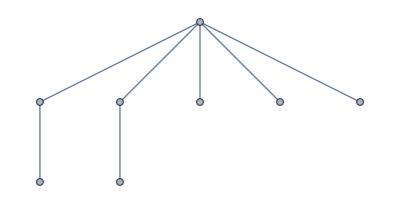
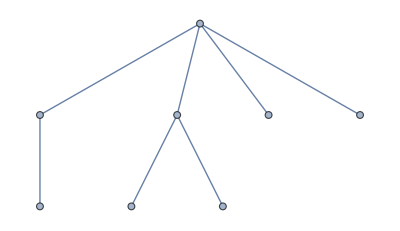

```mathematica
Take[samples,1]
```

```mathematica
SquaresInGraph[g_]:=Round[ N[Total[Map[#^4&,N[Eigenvalues[AdjacencyMatrix[g]]]]]]/4!]
```

```mathematica
possible = Select[samples,TrianglesInGraph2[First[#]]≥6&];
```

```mathematica
Length[possible]
```

681

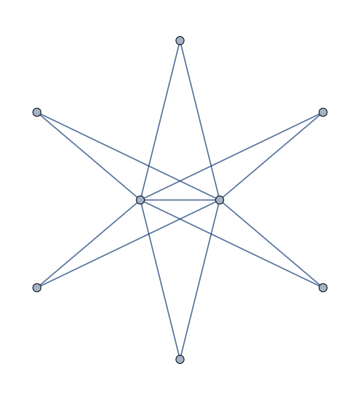
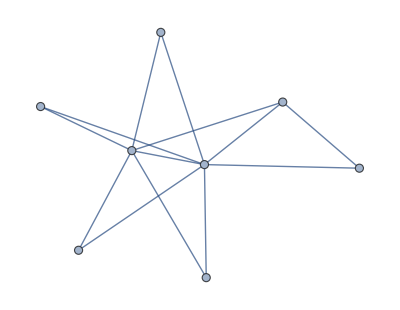
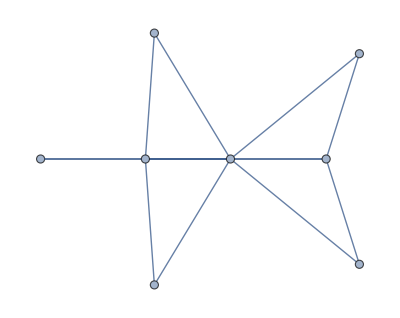
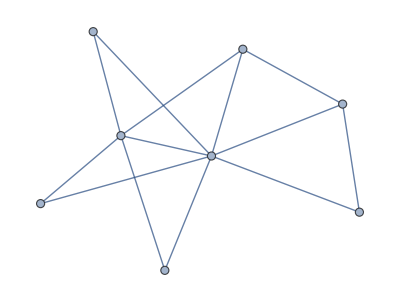
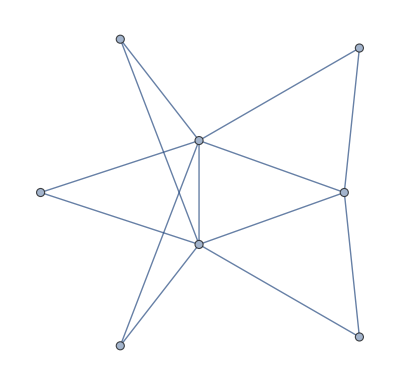
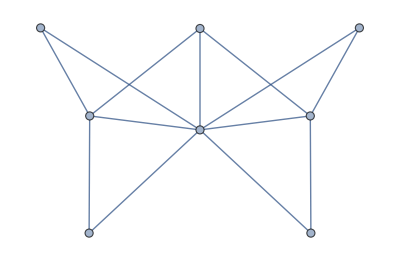
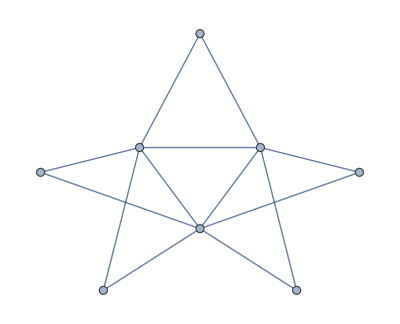
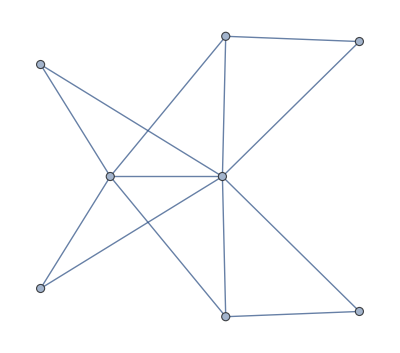

```mathematica
Map[IGLayoutGraphOpt[#,"MaxIterations"->10000]&,Take[possible,1]//First]
```

```mathematica
IGAdjacentTriangleCount[Graph[plantri[[8]]]]
```

{5,5,6,6,5,5,6,5,5,5,5,6,5,5,6,5,5}

```mathematica
Monitor[Table[Mean[Map[Table[Round[ N[Total[Map[#^k&,N[Eigenvalues[AdjacencyMatrix[#]]]]]]/k!],{k,{2,3}}]&,s]],{s,samples}],First[s]]
```

{{7,0},{8,1},{8,0},{9,2},{9,0},{10,3},{10,0},{11,4},{11,0},{12,5},{13,6},{9,1},{10,1},{11,1},{10,4},{8,0},{10,2},{11,5},{9,0},{10,2},{11,2},{12,6},{10,0},{11,3},{12,2},{13,7},{12,4},{14,8},{9,0},{10,0},{11,2},{10,0},{12,3},{12,2},{8,0},{9,1},{10,1},{11,3},{9,0},{10,2},{10,1},{11,1},{12,4},{12,3},{11,3},{11,1},{13,5},{13,3},{11,4},{12,7},{10,0},{11,2},{12,5},{12,4},{13,8},{11,0},{12,2},{13,6},{13,4},{14,9},{14,7},{14,4},{15,10},{10,0},{11,2},{11,0},{13,4},{10,0},{11,2},{11,0},{12,3},{12,2},{13,5},{11,1},{12,3},{12,2},{13,4},{13,3},{14,6},{14,5},{11,0},{12,3},{13,6},{14,10},{12,0},{13,4},{13,3},{14,7},{14,6},{15,11},{14,5},{15,8},{15,6},{16,12},{13,3},{14,4},{15,7},{13,0},{14,4},{15,8},{16,13},{15,5},{16,9},{17,14},{16,8},{17,10},{18,16},{10,2},{11,4},{9,0},{10,1},{12,5},{11,2},{12,2},{13,6},{9,1},{11,1},{11,2},{12,4},{11,1},{11,2},{13,5},{10,1},{11,3},{10,2},{11,4},{12,3},{13,6},{10,1},{10,1},{10,0},{10,1},{11,1},{12,3},{12,5},{12,2},{14,7},{10,0},{11,2},{12,4},{12,4},{13,7},{12,2},{14,8},{12,2},{13,5},{12,1},{13,4},{14,8},{13,2},{14,4},{15,9},{12,1},{11,2},{12,4},{12,4},{12,2},{13,3},{14,6},{11,1},{12,2},{12,3},{11,1},{12,1},{13,4},{13,5},{12,3},{12,2},{13,5},{13,4},{13,2},{14,6},{14,4},{15,8},{12,2},{13,3},{14,6},{13,1},{15,10},{14,2},{15,7},{16,10},{13,10},{12,5},{13,7},{14,11},{12,3},{13,5},{14,7},{15,12},{16,13},{9,0},{11,3},{10,1},{10,0},{11,2},{12,4},{11,1},{10,2},{12,2},{13,5},{11,2},{12,4},{11,1},{12,2},{13,5},{11,0},{14,6},{12,3},{13,5},{11,1},{13,4},{13,3},{15,8},{13,6},{14,9},{15,13},{11,1},{12,3},{12,4},{12,2},{13,4},{13,3},{14,7},{14,6},{15,10},{15,9},{16,14},{13,4},{14,5},{15,7},{16,11},{16,9},{17,15},{11,2},{11,2},{12,3},{12,2},{11,0},{12,3},{13,5},{12,1},{13,4},{14,7},{14,8},{13,3},{14,6},{15,10},{13,4},{13,2},{14,6},{12,2},{13,3},{13,3},{14,5},{14,4},{15,8},{15,9},{15,6},{16,11},{13,4},{13,3},{13,4},{13,2},{14,6},{14,5},{15,9},{13,3},{13,3},{13,2},{14,5},{15,7},{14,5},{15,7},{16,10},{14,3},{15,7},{16,11},{17,16},{16,8},{17,12},{18,17},{14,6},{14,5},{14,4},{15,7},{15,5},{16,9},{17,13},{14,4},{14,5},{15,6},{15,6},{16,9},{14,4},{14,3},{15,6},{16,11},{16,8},{16,7},{17,11},{17,11},{18,13},{19,19},{12,2},{13,4},{11,3},{12,2},{14,6},{14,7},{11,2},{10,0},{12,4},{11,0},{13,7},{12,1},{12,0},{13,2},{14,4},{15,8},{14,4},{15,6},{14,3},{15,8},{12,2},{12,2},{12,1},{13,4},{13,3},{13,2},{14,5},{14,7},{15,8},{14,4},{14,5},{13,2},{14,5},{15,7},{14,4},{15,6},{15,5},{16,9},{16,10},{16,8},{16,7},{17,12},{13,3},{11,3},{13,6},{12,3},{11,2},{12,5},{12,4},{13,6},{11,1},{11,1},{12,4},{12,3},{13,4},{14,7},{12,2},{13,5},{13,6},{13,3},{14,7},{13,5},{12,2},{13,4},{14,7},{13,5},{12,1},{13,3},{14,6},{14,5},{14,6},{15,7},{13,4},{13,5},{13,4},{13,3},{14,6},{14,6},{15,9},{14,5},{15,8},{14,5},{15,8},{16,12},{14,5},{15,7},{15,6},{16,9},{17,13},{12,2},{13,4},{13,3},{12,2},{12,3},{13,4},{13,5},{13,4},{14,6},{14,6},{13,2},{14,5},{15,8},{14,5},{14,6},{15,9},{13,3},{14,6},{14,4},{15,8},{14,6},{14,6},{14,4},{15,7},{14,3},{15,7},{15,6},{16,10},{12,2},{13,4},{13,2},{14,8},{15,7},{13,3},{13,2},{14,5},{14,5},{14,4},{15,7},{14,4},{15,6},{14,4},{14,4},{14,3},{15,6},{14,4},{14,5},{14,2},{15,5},{16,9},{15,4},{15,4},{16,8},{15,6},{16,8},{15,4},{17,12},{15,6},{15,7},{15,6},{15,6},{16,9},{15,5},{16,8},{16,7},{16,7},{17,11},{17,12},{17,10},{18,15},{17,10},{17,10},{17,9},{18,14},{13,3},{14,8},{15,12},{13,4},{15,8},{16,13},{13,2},{14,4},{15,6},{17,14},{13,5},{16,10},{16,16},{15,9},{16,12},{17,17},{16,10},{18,18},{16,9},{16,8},{13,2},{14,4},{16,9},{14,4},{15,8},{15,7},{16,11},{16,10},{17,15},{14,2},{15,5},{16,7},{17,10},{18,16},{15,6},{15,5},{15,6},{16,10},{17,14},{18,19},{16,8},{16,8},{17,11},{17,13},{17,11},{17,10},{18,15},{19,20},{15,5},{16,7},{16,6},{17,9},{18,13},{19,18},{18,14},{18,12},{18,11},{19,16},{20,22},{13,3},{14,4},{14,4},{15,6},{14,4},{14,5},{15,7},{15,6},{16,9},{15,7},{15,5},{16,9},{15,6},{15,5},{16,8},{15,8},{16,7},{15,6},{16,7},{16,6},{17,10},{17,11},{17,9},{18,14},{16,8},{16,7},{16,7},{17,11},{16,6},{17,9},{18,13},{18,12},{18,12},{19,17},{14,3},{17,10},{16,9},{16,10},{17,13},{17,12},{18,17},{15,3},{16,6},{17,10},{17,11},{17,9},{18,14},{19,18},{18,15},{19,22},{16,8},{18,13},{18,13},{20,23},{16,5},{16,6},{16,6},{17,8},{17,8},{17,7},{18,11},{18,13},{19,16},{19,15},{20,20},{19,17},{19,14},{19,14},{20,19},{21,25},{17,6},{18,9},{18,8},{19,12},{20,17},{21,22},{22,28},{12,4},{13,7},{14,10},{15,11},{11,2},{12,3},{12,3},{13,5},{13,4},{12,2},{13,4},{13,4},{14,7},{12,4},{12,3},{12,2},{13,5},{13,4},{14,6},{15,9},{16,13},{13,6},{14,8},{14,7},{15,10},{15,11},{16,13},{14,8},{14,5},{15,9},{16,11},{16,12},{17,14},{12,2},{13,4},{12,3},{13,3},{13,4},{14,6},{12,3},{13,4},{14,6},{14,5},{14,6},{14,4},{14,5},{15,8},{15,6},{16,10},{13,3},{13,3},{13,3},{13,4},{14,5},{14,7},{13,3},{14,5},{14,4},{15,7},{14,5},{14,4},{15,7},{15,6},{15,7},{16,10},{15,7},{16,10},{16,8},{17,11},{18,16},{15,7},{16,9},{17,14},{16,7},{14,6},{16,12},{15,10},{14,7},{17,16},{14,5},{15,8},{16,11},{17,13},{13,3},{14,5},{14,5},{16,10},{15,6},{15,7},{15,5},{16,9},{16,8},{17,12},{17,12},{18,15},{13,4},{13,4},{13,4},{14,5},{14,5},{15,8},{13,4},{13,3},{14,6},{14,5},{15,7},{14,4},{15,7},{15,7},{15,6},{16,10},{15,6},{15,6},{15,5},{16,9},{15,5},{16,8},{16,8},{17,12},{15,7},{15,9},{16,11},{15,8},{15,6},{16,10},{16,9},{17,13},{13,5},{14,7},{15,6},{16,9},{15,6},{15,5},{14,6},{15,9},{14,5},{16,12},{15,7},{17,13},{13,3},{14,5},{14,4},{14,4},{17,11},{16,9},{17,11},{16,8},{16,7},{17,11},{17,10},{17,10},{18,14},{18,15},{19,18},{17,9},{18,13},{13,2},{13,3},{14,3},{15,8},{16,10},{15,6},{16,9},{16,8},{17,12},{17,13},{16,7},{17,11},{17,10},{18,15},{15,6},{15,5},{15,4},{16,7},{17,13},{16,8},{17,11},{18,15},{18,14},{19,19},{16,9},{17,12},{18,17},{16,8},{17,10},{17,10},{17,9},{18,13},{16,7},{17,10},{16,7},{16,5},{17,9},{18,12},{18,11},{20,21},{19,15},{17,20},{18,21},{19,22},{17,14},{18,18},{19,23},{16,11},{16,12},{17,15},{17,12},{18,16},{18,15},{19,19},{20,24},{17,12},{18,14},{19,17},{19,18},{20,20},{21,26},{15,9},{16,12},{16,10},{14,4},{17,13},{11,2},{13,5},{12,1},{14,6},{12,3},{13,6},{16,10},{17,12},{17,11},{14,4},{15,6},{15,8},{14,3},{15,5},{16,9},{17,12},{16,7},{17,10},{18,15},{15,5},{17,11},{14,5},{14,4},{15,8},{17,14},{17,13},{18,15},{15,6},{16,7},{16,8},{16,8},{17,11},{16,7},{16,5},{17,9},{19,17},{16,7},{16,6},{17,9},{17,8},{18,12},{17,10},{17,9},{18,13},{19,17},{18,14},{18,17},{18,16},{19,21},{18,13},{20,22},{20,26},{19,17},{21,27},{16,7},{16,8},{17,11},{17,11},{17,10},{18,14},{17,12},{18,14},{16,10},{16,11},{18,13},{18,14},{18,12},{19,16},{17,10},{18,12},{18,11},{19,15},{20,20},{19,16},{19,14},{20,19},{21,24},{20,18},{20,18},{21,23},{22,29},{17,10},{14,3},{15,4},{16,7},{17,10},{17,11},{17,12},{18,14},{18,14},{19,17},{16,7},{16,7},{16,6},{17,9},{17,8},{18,12},{18,13},{18,13},{18,13},{19,16},{20,20},{19,16},{17,8},{18,12},{18,11},{18,11},{19,15},{21,24},{18,12},{18,13},{18,12},{19,16},{19,16},{19,15},{19,15},{17,10},{17,9},{18,13},{19,16},{18,14},{17,8},{19,18},{20,21},{17,9},{19,16},{19,14},{20,19},{18,10},{17,9},{18,10},{19,14},{19,16},{20,19},{19,14},{19,13},{20,18},{21,23},{20,18},{19,12},{20,16},{21,21},{22,26},{23,32},{15,6},{16,10},{17,13},{15,6},{16,8},{17,11},{18,14},{16,9},{18,16},{18,15},{19,18},{15,6},{15,5},{16,9},{16,8},{17,11},{18,12},{17,10},{17,10},{18,12},{18,14},{19,17},{16,8},{16,8},{17,11},{18,12},{19,14},{20,20},{19,17},{19,15},{18,11},{19,15},{19,16},{20,19},{19,15},{19,14},{20,19},{20,17},{21,23},{18,11},{19,14},{19,14},{20,18},{20,18},{20,19},{20,17},{21,22},{20,18},{20,20},{20,18},{20,17},{21,22},{22,27},{21,21},{19,20},{20,25},{20,21},{21,26},{19,17},{19,15},{21,22},{22,28},{21,30},{22,31},{21,23},{22,27},{23,33},{18,13},{19,17},{19,13},{19,13},{20,17},{21,22},{21,21},{22,26},{22,25},{23,31},{21,20},{21,21},{22,25},{23,30},{24,36},{20,16},{21,20},{22,24},{21,22},{22,25},{23,29},{22,24},{23,28},{24,34},{25,40},{17,12},{17,14},{17,13},{19,19},{20,23},{21,24},{18,12},{20,18},{22,28},{21,22},{21,23},{22,27},{21,21},{22,26},{23,31},{22,25},{21,21},{23,29},{24,35}}

```mathematica
Sort[Tally[%]]
```

{{0,32},{1,37},{2,72},{3,74},{4,98},{5,86},{6,89},{7,76},{8,66},{9,54},{10,55},{11,45},{12,44},{13,39},{14,35},{15,24},{16,23},{17,21},{18,17},{19,12},{20,11},{21,11},{22,11},{23,8},{24,6},{25,6},{26,6},{27,4},{28,4},{29,3},{30,2},{31,3},{32,1},{33,1},{34,1},{35,1},{36,1},{40,1}}

```mathematica
Mean[%]
```

{353/19,540/19}

```mathematica
TrianglesInGraph2[g_]:=Round[ N[Total[Map[#^3&,N[Eigenvalues[AdjacencyMatrix[g]]]]]]/6]
```

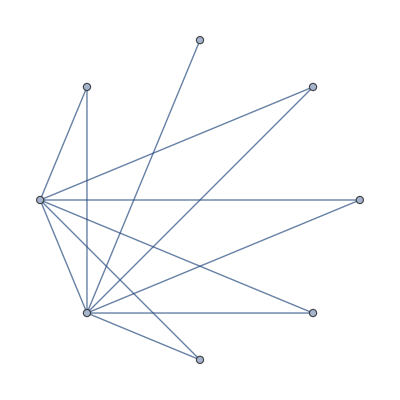
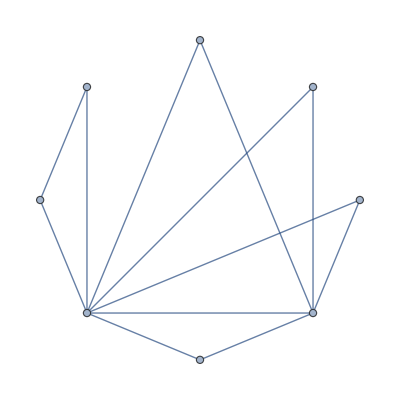
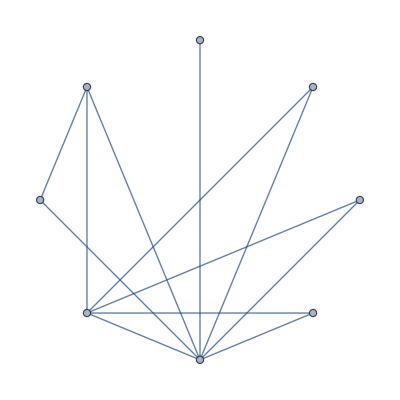
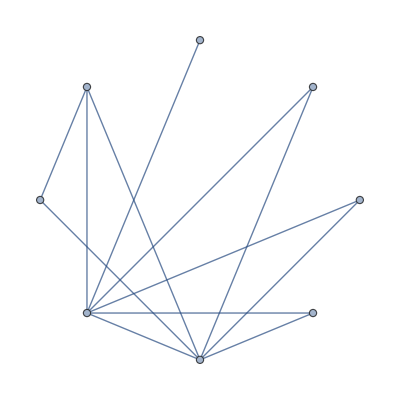
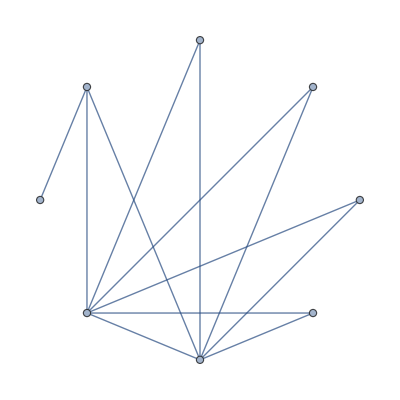
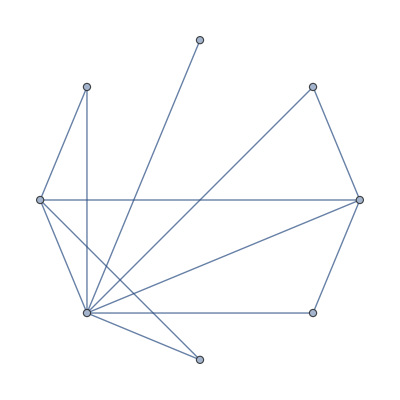
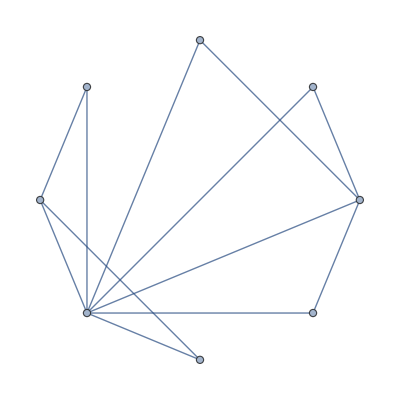
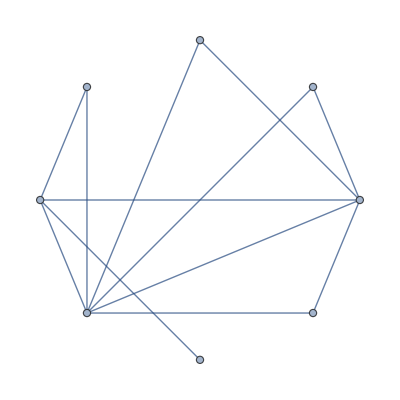
{-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5},-Graphics-{12,5}}

```mathematica
Map[Labeled[Graph[#,GraphLayout->"CircularEmbedding"],{EdgeCount[#],TrianglesInGraph2[#]}]&,samples[[10]]]
```

```mathematica
Map[ChromaticPolynomial[Graph[#],x]&,{{0<->4,0<->6,0<->7,1<->5,1<->7,2<->5,3<->6,3<->7,4<->0,4<->6,4<->7,5<->1,5<->2,5<->6,5<->7,6<->0,6<->3,6<->4,6<->5,7<->0,7<->1,7<->3,7<->4,7<->5},{0<->4,0<->6,0<->7,1<->4,1<->7,2<->5,2<->6,2<->7,3<->5,3<->7,4<->0,4<->1,4<->6,5<->2,5<->3,5<->7,6<->0,6<->2,6<->4,7<->0,7<->1,7<->2,7<->3,7<->5}}]//Tally
```

{{-44 x+188 x^2-335 x^3+324 x^4-185 x^5+63 x^6-12 x^7+x^8,1},{-64 x+240 x^2-384 x^3+344 x^4-188 x^5+63 x^6-12 x^7+x^8,1}}

```mathematica
Map[Graph[#,GraphLayout->"CircularEmbedding",VertexLabels->"Name"]->Labeled[FormulaGraphReverse[Fold[Plus,FindFullFormula[#]]],MaximalPlanarQ[#]->MoreInGraph3[#]]&,found5]
```

{-Graphics-→-Graphics-False→13,-Graphics-→-Graphics-False→13,-Graphics-→-Graphics-True→13,-Graphics-→-Graphics-True→13,-Graphics-→-Graphics-True→13}